```mathematica
ClearAll[α,d,ωR,ωE,μ,θ,κ,βR,βE,τ,P,R1,R2,R3,Er,i,YR,imax,θan]
```

```mathematica
imax=6; μ=48; d=0.00025;(*sets parameters*) (*from 2008 paper*)
(*d = death rate of RBCs - what about bystander killing? Cromer et al. est. is 0.0095 for first six days of infection*)
(*parasite clearance p = 0.0095*)
βR=0.000274 (*0.00015*); (*invasion rates - normo rate from 2008 paper*)
βE=0.00000183;

ωR=9;ωE=9;(*Burst sizes for reticulocytes and normocytes, from July 2017 paper *)

θ=0.1; θan=0.52509; (*recovery coefficient for erythropoesis, from 2008 paper*)

τ=2; (*lag time for erythropoesis, from 2008 paper*)
κ=6000000; (*steady state RBC density, from Cromer paper*)
Table[R1[i]=κ*0.0066,{i,-100,0}]; (*sets retics to be 3%*)
Table[R2[i]=κ*0.0066,{i,-100,0}];
Table[R3[i]=κ*0.0066,{i,-100,0}];
Table[Er[i]=κ*0.9802,{i,-100,0}];
Table[P[i]=0,{i,-100,-1}];
P[0] =684*9; (*10^5 infected RBCs, divided by 1462 μl per mouse, times 9 parasites per burst cell*)
```

```mathematica
0.000274/150
```

1.82667×10^-6

```mathematica
α=βR*(R1[i-1]+R2[i-1]+R3[i-1])+βE*Er[i-1]+μ;
YR=R1[i-1]+R2[i-1]+R3[i-1];
```

```mathematica
Pnext=(ωR*(YR*{1-Exp[(-P*βR)/α]})+ωE*Er*{1-Exp[(-P*βE)/α]})*(1-d);
R1next=θ*(κ-(R1+R2+R3+Er));
R2next=R1*Exp[(-P*βR)/α]*(1-d);
R3next=R2*Exp[(-P*βR)/α]*(1-d);
Enext=(Er*Exp[(-P*βE)/α]+R3*Exp[(-P*βR)/α])*(1-d);
```

```mathematica
Subiterate = {
P-> P[i-1],
R1-> R1[i-1],
R2-> R2[i-1],
R3->R3[i-1],
Er-> Er[i-1]};
```

```mathematica
Pnext /. Subiterate
R1next /. Subiterate
R2next /. Subiterate
R3next/. Subiterate
Enext/. Subiterate
```

```mathematica
For[i =1,i< imax,i++,
If[R1[i-1]+R2[i-1]+R3[i-1]+Er[i-1]<(0.5*κ),theta=θan, theta=θ];
P[i]={(1-d) ((1-ⅇ^(-(βR P[-1+i])/α)) YR ωR+(1-ⅇ^(-(βE P[-1+i])/α)) ωE Er[-1+i])};
R1[i]=theta (κ-Er[-1+i]-R1[-1+i]-R2[-1+i]-R3[-1+i]);
R2[i]=(1-d) ⅇ^(-(βR P[-1+i])/α) R1[-1+i];
R3[i]=(1-d) ⅇ^(-(βR P[-1+i])/α) R2[-1+i];
Er[i]=(1-d) (ⅇ^(-(βE P[-1+i])/α) Er[-1+i]+ⅇ^(-(βR P[-1+i])/α) R3[-1+i]);
];
ParaTab=Flatten[Table[P[i],{i,0,imax-1}]];
Retics=Flatten[Table[R1[i]+R2[i]+R3[i],{i,0,imax-1}]];
Normos=Flatten[Table[Er[i],{i,0,imax-1}]];
RBCtot=Retics+Normos;
ParaTabAdj=Flatten[Table[(Part[Retics,i]/Part[RBCtot,i])*βR+(Part[Normos,i]/Part[RBCtot,i])*βE, {i, 0, imax-1}]];
ParaTabRaw=Flatten[Table[(Part[Retics,i]/Part[RBCtot,i])*βE+(Part[Normos,i]/Part[RBCtot,i])*βE, {i, 0, imax-1}]];
```

Normocytes

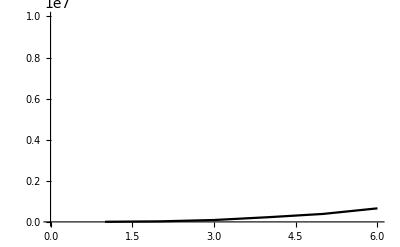

```mathematica
Print["Normocytes"]
ListPlot[{ParaTab}, Joined->True, PlotRange->{0,10000000},PlotStyle->{Black, Directive[Black, Dashing[0.01]]}] (*Data in dashed line*)
```

Number donor cells infected per microlitre (reticuloycte age preference)

```mathematica
(Part[Retics, 3]/Part[RBCtot,3]*βR+Part[Normos,3]/Part[RBCtot, 3]*βE)*8000000*0.036
```

0.998303

Number recipient cells infected per microlitre (reticulocyte age preference)

```mathematica
(Part[Retics,5]/Part[RBCtot, 5]*βR+Part[Normos,5]/Part[RBCtot,5]*βE)*8000000*0.964
```

15.7969

Number donor cells infected per microlitre (no age preference)

```mathematica
(Part[Retics, 3]/Part[RBCtot,3]*βE+Part[Normos,3]/Part[RBCtot, 3]*βE)*8000000*0.036
```

0.52704

Number recipient cells infected per microlitre (no age preference)

```mathematica
(Part[Retics,5]/Part[RBCtot, 5]*βE+Part[Normos,5]/Part[RBCtot,5]*βE)*8000000*0.964
```

14.113

Proportional increase in number cells infected without age preference

Donor cells

```mathematica
(0.419256-0.216)/0.216
```

0.941

Recipient cells

```mathematica
(6.19668-5.784)/5.784
```

0.0713485

```mathematica
{{(*# Cells infected per μL*), (*No age pref*), (*Retic pref*), (*% increase in inf. cell #*)}, {(*Donor, from day 3*), 0.419256, 0.216, 94.1%}, {(*Recipient, from day 5*), 6.19668, 5.784, 7.1%}}
```

```mathematica
ParaTab
```

{6156,26092.1,91420.8,228957.,387628.,659537.}

```mathematica
RBCtot
```

{6.×10^6,5.99344×10^6,5.96022×10^6,5.8218×10^6,5.21253×10^6,3.40849×10^6}

```mathematica
684*9
```

6156